```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\tmpra\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
(*
lineStyle={Thick,Black};
ln1=Line[{Log@{10.2,0.001},Log@{10.2,10^4}}];
ln2=Line[{Log@{20.4,0.001},Log@{20.4,10^4}}];
Text[Style["66 s",FontSize->Large],Log@{2,55}]
*)
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l-N[Log10[2]],u+N[Log10[2]],int}]],3];
tk22[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,2]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,3]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,4]],u,int}]~Join~
Table[{10^j,"",{N[c],d}},{j,l+N[Log[10,5]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,6]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,7]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,8]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,9]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,10]],u,int}]
],3];
tk23[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[2]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[3]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[4]],u,int}]~Join~
Table[{10^j,"",{N[c],d}},{j,l+N[Log10[5]],u,int}]
],3];
vtoe[v_]:=(v/0.437)^2;
etov[e_]:=0.437Sqrt[e];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

```mathematica
namev={(*Ignatovich1986-cf*)
{"D_2 (Liquid)",3.82},
{"D_2O",5.57},
{"^4He (Liquid)",1.6},
{"^6LiOH",2.6},
{"^6LiOH.H_2O",1.88},
{"LiF (Crystal)",4.71},
{"LiF (Natural)",3.23},
{"Be",6.89},
{"BeO",6.99},(*,Bodek2008-ag*)
{"C (Amorphous)",5.47},
{"Gr.C (Graphite)",6.11},
{"C (Diamond)",7.65},
{"CH (PolyEthyne)",2.59},
{"C_18H_14 (Terphenyl)",3.25},
{"CO_2",4.5},
{"Mg",3.37},
{"MgO",5.47},
{"Al",3.24},
{"Al_2O_3",5.13},
{"SiO_2 (Glass)",4.26},
{"SiC",5.11},
{"S_8 (Rhombic)",2.45},
{"^39Ar (Liquid)",5.85},
{"K_2O_3",4.0},
{"V_2O_3",3.94},
{"Cr",3.8},
{"Fe",6.34},
{"Stainless Steel",6.0},
{"Ni",6.84},
{"^58Ni",8.14},
{"Cu",5.66},
{"^65Cu",6.76},
{"CuO",5.69},
{"Cu_2O",4.85},
{"Zn",4.33},
{"ZnS",3.3},
{"Ga",4.34},
{"Ge",4.35},
{"Se",3.82},
{"Zr",3.85},
{"ZrH",2.2},
{"ZrH_1.8",0.60},
{"Sn (White)",3.38},
{"Te",2.92},
{"Dy",5.15},
{"^164Dy",8.76},
{"Ta",4.32},
{"Tl",3.94},
{"Pb",3.97},
{"Bi",3.34},
(**)
{"dPS",etov[161]},(*Bondar2017-fn*)
{"dPE",etov[209]},(*Bodek2008-ag*)
{"Ni(88%)-Mo(12%)",etov[229.5]},(*Bondar2017-fn*)
{"Ni(93%)-V(7%)",etov[210.1]},(*Bondar2017-fn*)
{"Ni↑↑-on-Si",etov[279]},(*Atchison2007-ol, η also has temperature dependence*)
{"DL.C-on-Si",etov[286]},(*Atchison2007-ol*)
{"Quartz",etov[95]},(*Bodek2008-ag*)
{"BN",etov[305]},(*Sobolev2010-da*)
{"Fomblin",etov[106.5]},(*Brose2012-ga*)
{"Ti",etov[50.2]},(*Brose2012-ga*)
{"^10B",etov[7.3]},(*Brose2012-ga*)
{"O_2 (Liquid)",etov[70]},(*Schorr1993-gr*)
{"PTFE (Teflon)",etov[123]}(*Schorr1993-gr,Bodek2008-ag*)
};
namee=MapAt[vtoe,namev,{All,2}];
namee//TableForm
sortnamee=Sort[namee,#1[[2]]<#2[[2]]&];
sz=Dimensions[namev][[1]];
```

D_2 (Liquid) | 76.4124
D_2O | 162.46
^4He (Liquid) | 13.4053
^6LiOH | 35.3984
^6LiOH.H_2O | 18.5077
LiF (Crystal) | 116.166
LiF (Natural) | 54.6314
Be | 248.585
BeO | 255.854
C (Amorphous) | 156.679
Gr.C (Graphite) | 195.488
C (Diamond) | 306.45
CH (PolyEthyne) | 35.1266
C_18H_14 (Terphenyl) | 55.31
CO_2 | 106.038
Mg | 59.4699
MgO | 156.679
Al | 54.9702
Al_2O_3 | 137.807
SiO_2 (Glass) | 95.029
SiC | 136.735
S_8 (Rhombic) | 31.4318
^39Ar (Liquid) | 179.204
K_2O_3 | 83.7832
V_2O_3 | 81.2886
Cr | 75.6144
Fe | 210.482
Stainless Steel | 188.512
Ni | 244.991
^58Ni | 346.965
Cu | 167.753
^65Cu | 239.293
CuO | 169.536
Cu_2O | 123.174
Zn | 98.1777
ZnS | 57.025
Ga | 98.6317
Ge | 99.0868
Se | 76.4124
Zr | 77.6173
ZrH | 25.3444
ZrH_1.8 | 1.88512
Sn (White) | 59.8233
Te | 44.6481
Dy | 138.884
^164Dy | 401.833
Ta | 97.7248
Tl | 81.2886
Pb | 82.5312
Bi | 58.4158
dPS | 161.
dPE | 209.
Ni(88%)-Mo(12%) | 229.5
Ni(93%)-V(7%) | 210.1
Ni↑↑-on-Si | 279.
DL.C-on-Si | 286.
Quartz | 95.
BN | 305.
Fomblin | 106.5
Ti | 50.2
^10B | 7.3
O_2 (Liquid) | 70.
PTFE (Teflon) | 123.

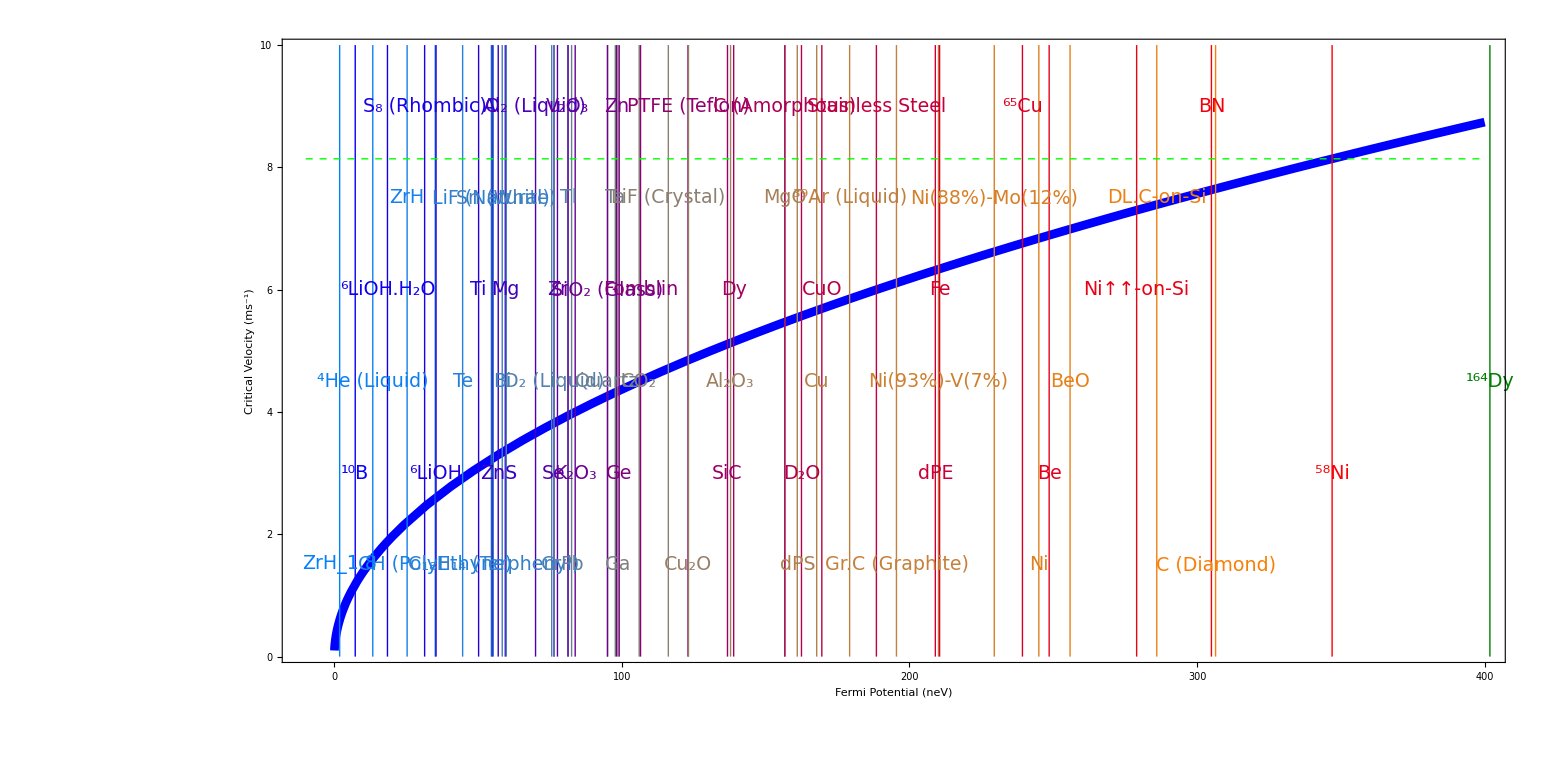

```mathematica
lineStyle={Thick,Dashed,Green};
lnucn=Line[{{-9.9,8.14},{399,8.14}}];
thk=.004;
epilog=ls=ln=txt=Table[{},{k,1,sz}];
For[i=1,i<=sz,i++,
ls[[i]]=Directive[{Thin,RGBColor[Mod[i/sz,1],Mod[i/2sz,1],Mod[1-i/sz,1]]}];
ln[[i]]=Line[{{sortnamee[[i]][[2]],0},{sortnamee[[i]][[2]],10}}];
txt[[i]]=Rotate[Text[Style[sortnamee[[i]][[1]],FontSize->19],{sortnamee[[i]][[2]],If[Mod[i,6]==1,1.5,If[Mod[i,6]==2,3,If[Mod[i,6]==3,4.5,If[Mod[i,6]==4,6,If[Mod[i,6]==5,7.5,9]]]]]}],90 Degree];
epilog[[i]]={ls[[i]],ln[[i]],txt[[i]]};
];
epi=Riffle[txt,ln];
epiac=Join[lineStyle,epi];
Plot[{etov[e]},{e,0,400},PlotStyle->{{Blue,Thickness[thk]}},PlotRange->{{-9.9,399},{0.1,9.9}},Frame->True,FrameLabel->{"Fermi Potential (neV)","Critical Velocity (ms^-1)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{48,Black},FrameTicksStyle->Thickness[thk],FrameStyle->Thickness[thk],ImageSize->1800,AspectRatio->1/2,
Epilog->{
epilog,
{Directive[lineStyle],lnucn}
}
]
```

## η-β of the above coating +: Means that the mentioned citation reflects the value within the heading citation. (*\cite{}*) means only this citation is used over the heading citation.

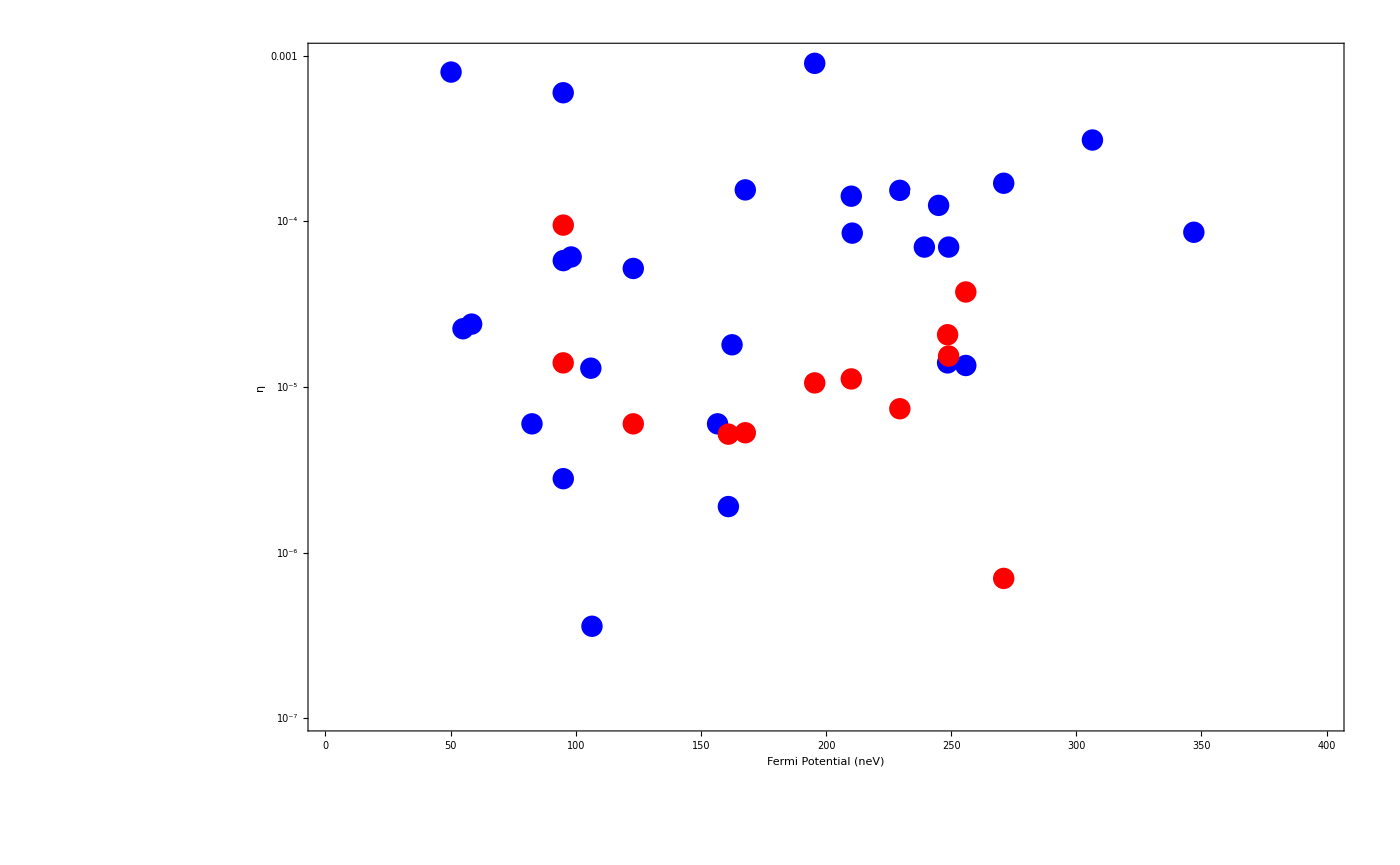

```mathematica
nameenb={(*Golub1991-ap*)
{"^58Ni",vtoe[8.14],8.6*10^-5,10^-8},
{"BeO",vtoe[6.99],1.35*10^-5,3.75*10^-5(*Serebrov2003-qo*)},
{"Ni",vtoe[6.84],12.5*10^-5(*+:Bondar2017-fn*),10^-8},
{"Be",vtoe[6.89],1.4*10^-5,2.07*10^-5(*Serebrov2003-qo*)},
{"^65Cu",vtoe[6.76],7.0*10^-5,10^-8},
{"Fe",vtoe[6.34],8.5*10^-5,10^-8},
{"C",vtoe[5.47],0.6*10^-5,10^-8},
{"Cu",vtoe[5.66],15.5*10^-5(*+:Bondar2017-fn*),0.53*10^-5(*Chesnevskaya2007-jq,+:Serebrov2003-qo*)},
{"Pb",vtoe[3.97],0.6*10^-5,10^-8},
{"Al",vtoe[3.24],2.25*10^-5,10^-8},
(*Ignatovich1986-cf, always use something else*)
{"SiO_2",vtoe[4.26],0.28*10^-5,9.5*10^-5(*Serebrov2000-kt*)},
{"B-SiO_2",vtoe[4.26],5.8*10^-5,10^-8},
{"PTFE",123,5.2*10^-5,.6*10^-5(*Serebrov2003-qo*)},
{"Bi",vtoe[3.34],2.4*10^-5,10^-8},
{"CO_2",vtoe[4.5],1.3*10^-5,10^-8},
{"D_2O",vtoe[5.57],1.8*10^-5,10^-8},
{"Zn",vtoe[4.33],6.1*10^-5,10^-8},
(*Chesnevskaya2007-jq*)
{"NiMo",229.5,1.54*10^-4(*+:Bondar2017-fn*),0.74*10^-5},
{"NiV",210.1,1.42*10^-4(*Bondar2017-fn*),1.12*10^-5},
{"dPS",161,.19*10^-5(*Bondar2017-fn*),0.52*10^-5},
(*Atchison2006-th*)
{"Di.C",vtoe[7.65],3.1*10^-4,10^-8},
(*Brose2012-ga*)
{"Fomblin",106.5,3.6*10^-7,10^-8},
{"^10B",7.3,5.356,10^-8},
{"Ti",50.2,7.97*10^-4,10^-8},
(*Serebrov2003-qo*)
{"Gr.C",vtoe[6.11],9*10^-4(*Serebrov2000-kt*),1.06*10^-5},
(*Serebrov2000-kt*)
{"Quartz",95(*Bodek2008-ag*),5.98*10^-4,1.4*10^-5},
{"DL.C-on-Al",271(*Atchison2007-uz*),1.7*10^-4,0.7*10^-6}(*Atchison2005-ni,Atchison2007-tj*),
{"DL.C-on-PET",249(*Atchison2007-uz*),0.7*10^-4,15.4*10^-6}(*Atchison2005-ni,Atchison2007-tj*)
(*{"D_2 (Liquid)",3.82},
{"^4He (Liquid)",1.6},
{"^6LiOH",2.6},
{"^6LiOH.H_2O",1.88},
{"LiF (Crystal)",4.71},
{"LiF (Natural)",3.23},
{"CH (PolyEthyne)",2.59},
{"C_18H_14 (Terphenyl)",3.25},
{"Mg",3.37},
{"MgO",5.47},
{"Al_2O_3",5.13},
{"SiC",5.11},
{"S_8 (Rhombic)",2.45},
{"^39Ar (Liquid)",5.85},
{"K_2O_3",4.0},
{"V_2O_3",3.94},
{"Cr",3.8},
{"Stainless Steel",6.0},
{"CuO",5.69},
{"Cu_2O",4.85},
{"ZnS",3.3},
{"Ga",4.34},
{"Ge",4.35},
{"Se",3.82},
{"Zr",3.85},
{"ZrH",2.2},
{"ZrH_1.8",0.60},
{"Sn (White)",3.38},
{"Te",2.92},
{"Dy",5.15},
{"^164Dy",8.76},
{"Ta",4.32},
{"Tl",3.94},
(**)
{"dPE",etov[209]},(*Bodek2008-ag*)
{"Ni↑↑-on-Si",etov[279]},(*Atchison2007-ol, η also has temperature dependence*)
{"BN",etov[305]},(*Sobolev2010-da*)
{"O_2 (Liquid)",etov[70]},(*Schorr1993-gr*)
*)
};
sortenb=Sort[nameenb,#1[[2]]<#2[[2]]&];
szenb=Dimensions[sortenb][[1]];
lineStyle1={PointSize[.01],Blue};
lineStyle2={PointSize[.01],Red};
thk=.004;
epilog1=epilog2=ln1=ln2=txt1=txt2=callout1=callout2=Table[{},{k,1,szenb}];
For[i=1,i<=szenb,i++,
(*ls[[i]]=Directive[{Thin,RGBColor[Mod[i/sz,1],Mod[i/2sz,1],Mod[1-i/sz,1]]}];*)
ln1[[i]]=Point[{sortenb[[i]][[2]],Log@sortenb[[i]][[3]]}];
ln2[[i]]=Point[{sortenb[[i]][[2]],Log@sortenb[[i]][[4]]}];
txt1[[i]]=Text[Style[sortenb[[i]][[1]],FontSize->19],{sortenb[[i]][[2]]+If[Mod[i,2]==1,20,-20],Log@(sortenb[[i]][[3]]*If[Mod[i,2]==1,0.9,1/.9])}];
txt2[[i]]=Text[Style[sortenb[[i]][[1]],FontSize->19],{sortenb[[i]][[2]]+If[Mod[i,2]==1,20,-20],Log@(sortenb[[i]][[4]]*If[Mod[i,2]==1,0.9,1/.9])}];
epilog1[[i]]={ln1[[i]],txt1[[i]]};
epilog2[[i]]={ln2[[i]],txt2[[i]]};
callout1[[i]]=Callout[{sortenb[[i]][[2]],sortenb[[i]][[3]]},sortenb[[i]][[1]],Appearance->"Frame",Background->Blue,LabelStyle->{White,Large},CalloutStyle->{White,Blue}];
callout2[[i]]=Callout[{sortenb[[i]][[2]],sortenb[[i]][[4]]},sortenb[[i]][[1]],Appearance->"Frame",Background->Red,LabelStyle->{White,Large},CalloutStyle->{White,Red}];
];
epi1=Riffle[txt1,ln1];
epiac1=Join[lineStyle1,epi1];
epi2=Riffle[txt2,ln2];
epiac2=Join[lineStyle2,epi2];
ListLogPlot[{callout1,callout2},PlotStyle->{Blue,Red},PlotRange->{{1,399},{1.01*10^-7,0.99*10^-3}},Frame->True,FrameLabel->{{"η","β"},{"Fermi Potential (neV)",""}},FrameStyle->{{Blue,Red},{Black,Black}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicks->{(*y,x*){tk22[-7,-2,.02,0,0.015,0,1],tk22[-7,-2,.02,0,0.015,0,1]},{LinTicks,LinTicks}},FrameTicksStyle->{{Directive[Blue,Thickness[thk/2]],Directive[Red,Thickness[thk/2]]},{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]}},
ImageSize->1400
]
```

```mathematica
Show[{ListLogPlot[Partition[N[sortenb[[;;,{2,3}]]],1],PlotLabels->Placed[sortenb[[;;,1]],Automatic],PlotStyle->Blue,PlotRange->{{1,399},{1.01*10^-7,0.99*10^-3}},Frame->True,FrameLabel->{{"η","β"},{"Fermi Potential (neV)",""}},FrameStyle->{{Blue,Red},{Black,Black}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicks->{(*y,x*){tk22[-7,-2,.02,0,0.015,0,1],tk22[-7,-2,.02,0,0.015,0,1]},{LinTicks,LinTicks}},FrameTicksStyle->{{Directive[Blue,Thickness[thk/2]],Directive[Red,Thickness[thk/2]]},{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]}},
ImageSize->1200
],
ListLogPlot[Partition[N[sortenb[[;;,{2,4}]]],1],PlotLabels->Placed[sortenb[[;;,1]],Automatic],PlotStyle->Red,PlotRange->{{1,399},{1.01*10^-7,0.99*10^-3}},Frame->True,FrameLabel->{{"η","β"},{"Fermi Potential (neV)",""}},FrameStyle->{{Blue,Red},{Black,Black}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicks->{(*y,x*){tk22[-7,-2,.02,0,0.015,0,1],tk22[-7,-2,.02,0,0.015,0,1]},{LinTicks,LinTicks}},FrameTicksStyle->{{Directive[Blue,Thickness[thk/2]],Directive[Red,Thickness[thk/2]]},{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]}},
ImageSize->1200
]}]
```